```mathematica
Propagation simulation through angular spectrum representation
```

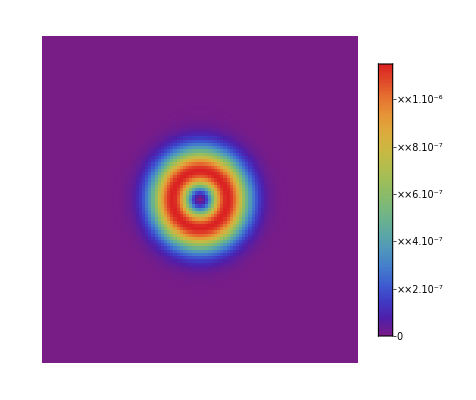

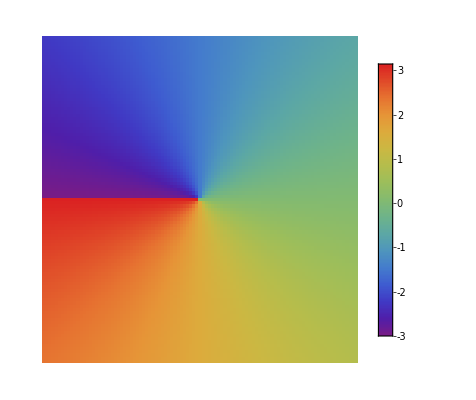

```mathematica
λ=500*^-9;(*wavelength*)
k=(2 π)/λ;(*wavenumber*)
w0=5*^-3;(*beam waist*)
zr=(π w0^2)/λ;(*Rayleigh Range*)
min=-20*^-3;max=20*^-3;step=100;(*array dimensions*)
d=(max-min)/step;(*step size*)
input2d=Table[ Exp[-((√(x^2+y^2))/w0)^2 ]BesselJ[1,√(x^2+y^2)]Exp[I Arg[Complex[y,x]]],{x,Range[min,max,d]},{y,Range[min,max,d]}];(*initial field*)
index=Table[{x,y},{x,Range[-step/2,step/2]},{y,Range[-step/2,step/2]}];(*coordinates required for k_z calculation*)
(*index1=Table[{x,y},{x,Range[min,max,d]},{y,Range[min,max,d]}];*)
ArrayPlot[Abs[input2d]^2,PlotLegends->Automatic,DataRange->{{min,max},{min,max}},FrameTicks->All,ColorFunction->"Rainbow"]
ArrayPlot[Arg[input2d],PlotLegends->Automatic,DataRange->{{min,max},{min,max}},FrameTicks->All,ColorFunction->"Rainbow",PlotRange->All]
```

```mathematica
Clear[input2d]
```

```mathematica
input2d1=Import["/Users/davidlafferty/Projects/vbeams/Mathematica/output/zrad_real.csv","CSV"];
input2d2=Import["/Users/davidlafferty/Projects/vbeams/Mathematica/output/zrad_imag.csv","CSV"];
```

```mathematica
input2d=input2d1+(I*input2d2)
```

{{-7.26682+259.672 ⅈ,-30.7605+265.813 ⅈ,-53.63+265.555 ⅈ,-75.3068+258.887 ⅈ,-95.2635+245.961 ⅈ,-113.027+227.08 ⅈ,89,-113.027+227.08 ⅈ,-95.2635+245.961 ⅈ,-75.3068+258.887 ⅈ,-53.63+265.555 ⅈ,-30.7605+265.813 ⅈ,-7.26682+259.672 ⅈ},99,{1}}
 |  |  |  |

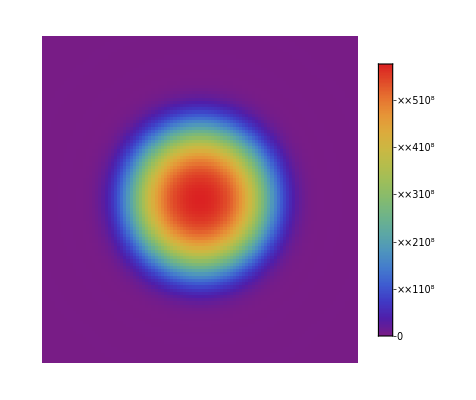

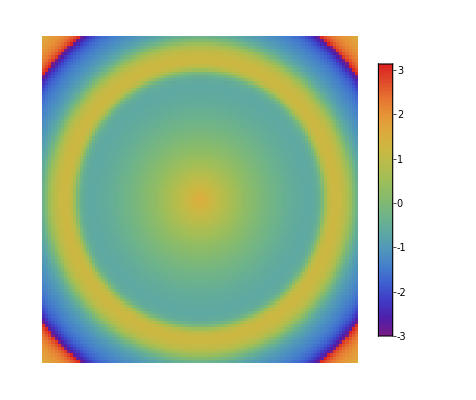

```mathematica
ArrayPlot[Abs[input2d]^2,PlotLegends->Automatic,DataRange->{{min,max},{min,max}},FrameTicks->All,ColorFunction->"Rainbow"]
ArrayPlot[Arg[input2d],PlotLegends->Automatic,DataRange->{{min,max},{min,max}},FrameTicks->All,ColorFunction->"Rainbow",PlotRange->All]
```

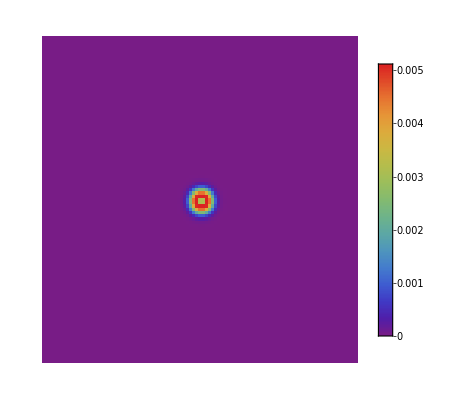

```mathematica
fw=Fourier[input2d*(-1)^Table[i+j,{i,Length[input2d]},{j,Length[input2d]}],FourierParameters->{0,1}];(*fourier transform to k-space*)
ArrayPlot[Abs[fw],PlotLegends->Automatic,PlotRange->All, FrameTicks->All,ColorFunction->"Rainbow"]
```

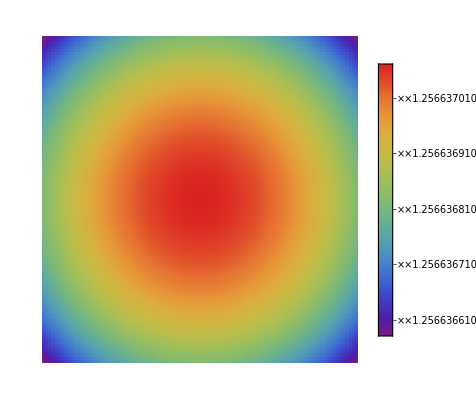

```mathematica
kz=Table[√(k^2-((2 π index[[i,j,1]])/(max-min))^2-((2 π index[[i,j,2]])/(max-min))^2),{i,1,Length[index]},{j,1,Length[index]}];(*calculate k_z for each (k_x,k_y) point*)
ArrayPlot[kz,PlotLegends->Automatic,DataRange->{{-step/(2(max-min)),step/(2(max-min))},{-step/(2(max-min)),step/(2(max-min))}},PlotRange->All, FrameTicks->All,ColorFunction->"Rainbow"]
```

```mathematica
(*kz1=Table[√(k^2-(k Cos[ToPolarCoordinates[index1[[i,j]]][[2]]]/(2 π/ ToPolarCoordinates[index1[[i,j]]][[1]]))^2-(k Sin[ToPolarCoordinates[index1[[i,j]]][[2]]]/(2 π/ToPolarCoordinates[index1[[i,j]]][[1]]))^2),{i,1,Length[index1]},{j,1,Length[index1]}];*)
```

```mathematica
output2d=Table[InverseFourier[fw*Exp[I kz z],FourierParameters->{0,1}],{z,Range[0,zr,zr/20]}];(*propagate then inverse FT*)
```

```mathematica
Manipulate[ArrayPlot[Abs[output2d[[z,All,All]]]^2,PlotLegends->Automatic,DataRange->{{min,max},{min,max}},FrameTicks->All,ColorFunction->"Rainbow"],{z,1,Length[output2d],1}]
```